{{1,10},{2,15},{3,45},{5,30}}

FittedModel[…]

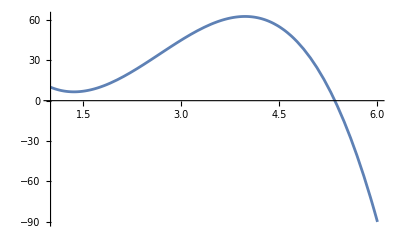

```mathematica
data = {{1, 10}, {2, 15}, {3, 45}, {5, 30}}
model = NonlinearModelFit[data, a x^3 + b x^2 + c x + d, {a, b, c, d}, x]
Plot[model[x], {x, 1, 6}]
```

```mathematica
Show[ListPlot[data, ], ]
```